Cylindrical

positive Right side weights

Left Positive side Weights

After flux

complex number

3

1.45

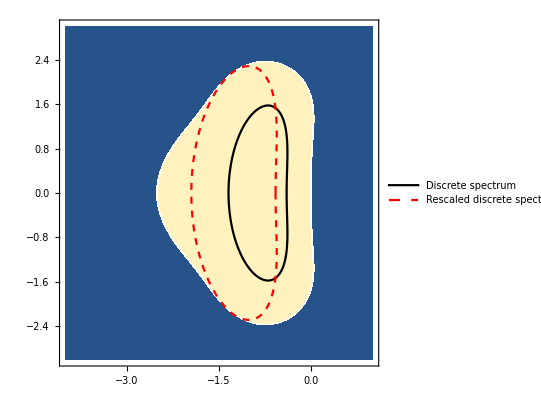

5

1.52

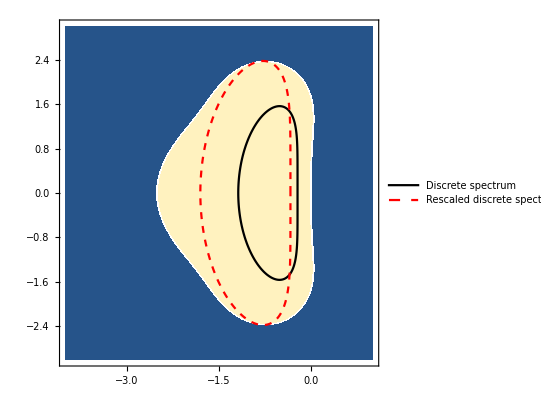

10

1.52

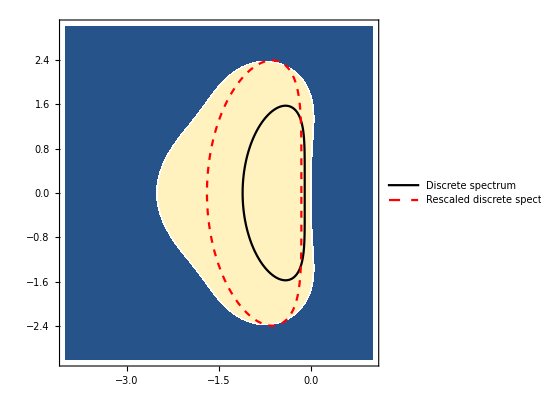

20

1.5

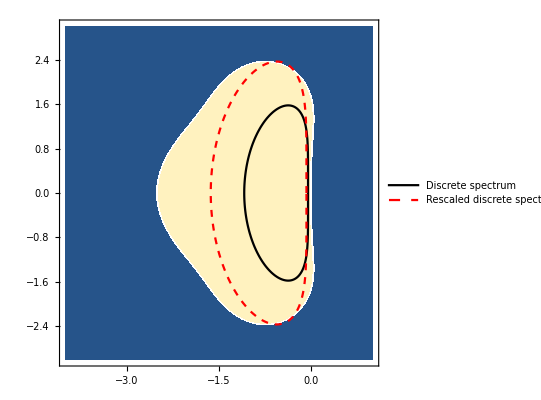

50

1.48

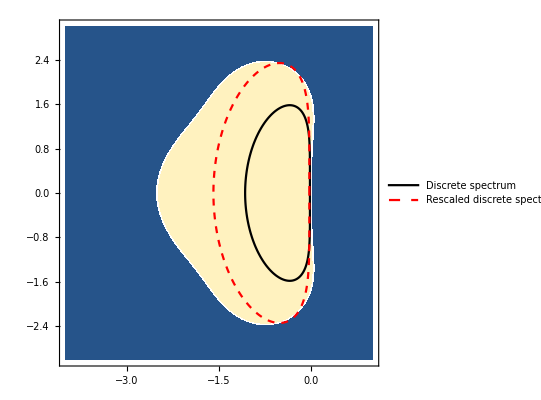

100

1.46

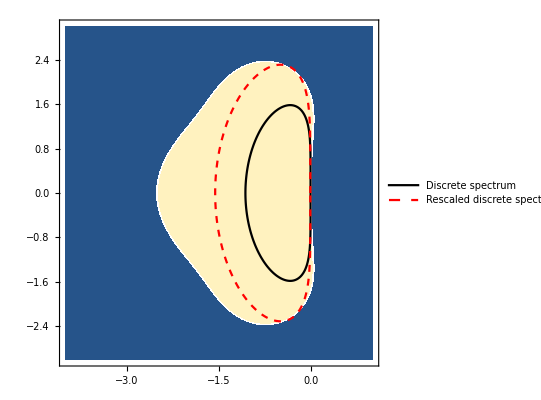

```mathematica
(* Modified von-Neumann stability analysis [Liu,H.and Jiao,X., Journal of Computational Physics,314,pp.749-773, 2016.] for WENO-C 
[Shadab,M.A. et al, arXiv preprint arXiv:1711.06212, 2017.] 
  Coder: Mohammad Afzal Shadab
Email: afzalshadab0@yahoo.com
Last edited: May 11, 2019
*)

(*  Cartesian
Right side positive weights

Clear["Global`*"]

M11=1;
M21=1/2*((i-2+1/2)^2-(i-2-1/2)^2)/((i-2+1/2)-(i-2-1/2));
M31=1/3*((i-2+1/2)^3-(i-2-1/2)^3)/((i-2+1/2)-(i-2-1/2));
M41=1/4*((i-2+1/2)^4-(i-2-1/2)^4)/((i-2+1/2)-(i-2-1/2));
M51=1/5*((i-2+1/2)^5-(i-2-1/2)^5)/((i-2+1/2)-(i-2-1/2));

M12=1;
M22=1/2*((i-1+1/2)^2-(i-1-1/2)^2)/((i-1+1/2)-(i-1-1/2));
M32=1/3*((i-1+1/2)^3-(i-1-1/2)^3)/((i-1+1/2)-(i-1-1/2));
M42=1/4*((i-1+1/2)^4-(i-1-1/2)^4)/((i-1+1/2)-(i-1-1/2));
M52=1/5*((i-1+1/2)^5-(i-1-1/2)^5)/((i-1+1/2)-(i-1-1/2));

M13=1;
M23=1/2*((i+1/2)^2-(i-1/2)^2)/((i+1/2)-(i-1/2));
M33=1/3*((i+1/2)^3-(i-1/2)^3)/((i+1/2)-(i-1/2));
M43=1/4*((i+1/2)^4-(i-1/2)^4)/((i+1/2)-(i-1/2));
M53=1/5*((i+1/2)^5-(i-1/2)^5)/((i+1/2)-(i-1/2));

M14=1;
M24=1/2*((i+1+1/2)^2-(i+1-1/2)^2)/((i+1+1/2)-(i+1-1/2));
M34=1/3*((i+1+1/2)^3-(i+1-1/2)^3)/((i+1+1/2)-(i+1-1/2));
M44=1/4*((i+1+1/2)^4-(i+1-1/2)^4)/((i+1+1/2)-(i+1-1/2));
M54=1/5*((i+1+1/2)^5-(i+1-1/2)^5)/((i+1+1/2)-(i+1-1/2));

M15=1;
M25=1/2*((i+2+1/2)^2-(i+2-1/2)^2)/((i+2+1/2)-(i+2-1/2));
M35=1/3*((i+2+1/2)^3-(i+2-1/2)^3)/((i+2+1/2)-(i+2-1/2));
M45=1/4*((i+2+1/2)^4-(i+2-1/2)^4)/((i+2+1/2)-(i+2-1/2));
M55=1/5*((i+2+1/2)^5-(i+2-1/2)^5)/((i+2+1/2)-(i+2-1/2));


b1=1;
b2=i+1/2;
b3=(i+1/2)^2;
b4=(i+1/2)^3;
b5=(i+1/2)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  
cylR=Simplify[Inverse[A1].b];


Left side Positive Weights

M11=1;
M21=1/2*((i-1-2+1/2)^2-(i-1-2-1/2)^2)/((i-1-2+1/2)-(i-1-2-1/2));
M31=1/3*((i-1-2+1/2)^3-(i-1-2-1/2)^3)/((i-1-2+1/2)-(i-1-2-1/2));
M41=1/4*((i-1-2+1/2)^4-(i-1-2-1/2)^4)/((i-1-2+1/2)-(i-1-2-1/2));
M51=1/5*((i-1-2+1/2)^5-(i-1-2-1/2)^5)/((i-1-2+1/2)-(i-1-2-1/2));

M12=1;
M22=1/2*((i-1-1+1/2)^2-(i-1-1-1/2)^2)/((i-1-1+1/2)-(i-1-1-1/2));
M32=1/3*((i-1-1+1/2)^3-(i-1-1-1/2)^3)/((i-1-1+1/2)-(i-1-1-1/2));
M42=1/4*((i-1-1+1/2)^4-(i-1-1-1/2)^4)/((i-1-1+1/2)-(i-1-1-1/2));
M52=1/5*((i-1-1+1/2)^5-(i-1-1-1/2)^5)/((i-1-1+1/2)-(i-1-1-1/2));

M13=1;
M23=1/2*((i-1+1/2)^2-(i-1-1/2)^2)/((i-1+1/2)-(i-1-1/2));
M33=1/3*((i-1+1/2)^3-(i-1-1/2)^3)/((i-1+1/2)-(i-1-1/2));
M43=1/4*((i-1+1/2)^4-(i-1-1/2)^4)/((i-1+1/2)-(i-1-1/2));
M53=1/5*((i-1+1/2)^5-(i-1-1/2)^5)/((i-1+1/2)-(i-1-1/2));

M14=1;
M24=1/2*((i-1+1+1/2)^2-(i-1+1-1/2)^2)/((i-1+1+1/2)-(i-1+1-1/2));
M34=1/3*((i-1+1+1/2)^3-(i-1+1-1/2)^3)/((i-1+1+1/2)-(i-1+1-1/2));
M44=1/4*((i-1+1+1/2)^4-(i-1+1-1/2)^4)/((i-1+1+1/2)-(i-1+1-1/2));
M54=1/5*((i-1+1+1/2)^5-(i-1+1-1/2)^5)/((i-1+1+1/2)-(i-1+1-1/2));

M15=1;
M25=1/2*((i-1+2+1/2)^2-(i-1+2-1/2)^2)/((i-1+2+1/2)-(i-1+2-1/2));
M35=1/3*((i-1+2+1/2)^3-(i-1+2-1/2)^3)/((i-1+2+1/2)-(i-1+2-1/2));
M45=1/4*((i-1+2+1/2)^4-(i-1+2-1/2)^4)/((i-1+2+1/2)-(i-1+2-1/2));
M55=1/5*((i-1+2+1/2)^5-(i-1+2-1/2)^5)/((i-1+2+1/2)-(i-1+2-1/2));


b1=1;
b2=i-1+1/2;
b3=(i-1+1/2)^2;
b4=(i-1+1/2)^3;
b5=(i-1+1/2)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  
cylL=Simplify[Inverse[A1].b];

After flux
oye
WRminus2=Part[cylR,1];
WRminus1=Part[cylR,2];
WRminus0=Part[cylR,3];
WRplus1=Part[cylR,4];
WRplus2=Part[cylR,5];

WLminus2=Part[cylL,1];
WLminus1=Part[cylL,2];
WLminus0=Part[cylL,3];
WLplus1=Part[cylL,4];
WLplus2=Part[cylL,5];

K1=Simplify[-WLminus2];
K2=Simplify[WRminus2-WLminus1];
K3=Simplify[WRminus1-WLminus0];
K4=Simplify[WRminus0-WLplus1];
K5=Simplify[WRplus1-WLplus2];
K6=Simplify[WRplus2];

clear[i];

complex number
f[angle_]:=-Simplify[(K1*(Cos[3*angle]+I*Sin[3*angle])+K2*(Cos[2*angle]+I*Sin[2*angle])+ K3*(Cos[1*angle]+I*Sin[1*angle])+ K4*1+ K5*(Cos[1*angle]-I*Sin[1*angle])+ K6*(Cos[2*angle]-I*Sin[2*angle]))]

ParametricPlot[ReIm[f],{angle,0,2Pi},Frame->True, FrameLabel->{Style["Re(-z)",10],Style["Im(-z)",10]},PlotTheme->"Scientific"]


sigma=1.44
GG[angle_]:=sigma*f[angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[f[angle]]},{ReIm[GG[angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]
Clear["Global`*"]
*)
Cylindrical

Right side positive weights

Clear[i]

M11=1;
M21=2/3*((i-2)^3-(i-2-1)^3)/((i-2)^2-(i-2-1)^2);
M31=2/4*((i-2)^4-(i-2-1)^4)/((i-2)^2-(i-2-1)^2);
M41=2/5*((i-2)^5-(i-2-1)^5)/((i-2)^2-(i-2-1)^2);
M51=2/6*((i-2)^6-(i-2-1)^6)/((i-2)^2-(i-2-1)^2);

M12=1;
M22=2/3*((i-1)^3-(i-1-1)^3)/((i-1)^2-(i-1-1)^2);
M32=2/4*((i-1)^4-(i-1-1)^4)/((i-1)^2-(i-1-1)^2);
M42=2/5*((i-1)^5-(i-1-1)^5)/((i-1)^2-(i-1-1)^2);
M52=2/6*((i-1)^6-(i-1-1)^6)/((i-1)^2-(i-1-1)^2);

M13=1;
M23=2/3*((i)^3-(i-1)^3)/((i)^2-(i-1)^2);
M33=2/4*((i)^4-(i-1)^4)/((i)^2-(i-1)^2);
M43=2/5*((i)^5-(i-1)^5)/((i)^2-(i-1)^2);
M53=2/6*((i)^6-(i-1)^6)/((i)^2-(i-1)^2);

M14=1;
M24=2/3*((i+1)^3-(i+1-1)^3)/((i+1)^2-(i+1-1)^2);
M34=2/4*((i+1)^4-(i+1-1)^4)/((i+1)^2-(i+1-1)^2);
M44=2/5*((i+1)^5-(i+1-1)^5)/((i+1)^2-(i+1-1)^2);
M54=2/6*((i+1)^6-(i+1-1)^6)/((i+1)^2-(i+1-1)^2);

M15=1;
M25=2/3*((i+2)^3-(i+2-1)^3)/((i+2)^2-(i+2-1)^2);
M35=2/4*((i+2)^4-(i+2-1)^4)/((i+2)^2-(i+2-1)^2);
M45=2/5*((i+2)^5-(i+2-1)^5)/((i+2)^2-(i+2-1)^2);
M55=2/6*((i+2)^6-(i+2-1)^6)/((i+2)^2-(i+2-1)^2);

b1=1;
b2=i;
b3=(i)^2;
b4=(i)^3;
b5=(i)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  
cylR=Simplify[Inverse[A1].b];

Left side Positive Weights

M11=1;
M21=2/3*((i-1-2)^3-(i-1-2-1)^3)/((i-1-2)^2-(i-1-2-1)^2);
M31=2/4*((i-1-2)^4-(i-1-2-1)^4)/((i-1-2)^2-(i-1-2-1)^2);
M41=2/5*((i-1-2)^5-(i-1-2-1)^5)/((i-1-2)^2-(i-1-2-1)^2);
M51=2/6*((i-1-2)^6-(i-1-2-1)^6)/((i-1-2)^2-(i-1-2-1)^2);

M12=1;
M22=2/3*((i-1-1)^3-(i-1-1-1)^3)/((i-1-1)^2-(i-1-1-1)^2);
M32=2/4*((i-1-1)^4-(i-1-1-1)^4)/((i-1-1)^2-(i-1-1-1)^2);
M42=2/5*((i-1-1)^5-(i-1-1-1)^5)/((i-1-1)^2-(i-1-1-1)^2);
M52=2/6*((i-1-1)^6-(i-1-1-1)^6)/((i-1-1)^2-(i-1-1-1)^2);

M13=1;
M23=2/3*((i-1)^3-(i-1-1)^3)/((i-1)^2-(i-1-1)^2);
M33=2/4*((i-1)^4-(i-1-1)^4)/((i-1)^2-(i-1-1)^2);
M43=2/5*((i-1)^5-(i-1-1)^5)/((i-1)^2-(i-1-1)^2);
M53=2/6*((i-1)^6-(i-1-1)^6)/((i-1)^2-(i-1-1)^2);

M14=1;
M24=2/3*((i-1+1)^3-(i-1+1-1)^3)/((i-1+1)^2-(i-1+1-1)^2);
M34=2/4*((i-1+1)^4-(i-1+1-1)^4)/((i-1+1)^2-(i-1+1-1)^2);
M44=2/5*((i-1+1)^5-(i-1+1-1)^5)/((i-1+1)^2-(i-1+1-1)^2);
M54=2/6*((i-1+1)^6-(i-1+1-1)^6)/((i-1+1)^2-(i-1+1-1)^2);

M15=1;
M25=2/3*((i-1+2)^3-(i-1+2-1)^3)/((i-1+2)^2-(i-1+2-1)^2);
M35=2/4*((i-1+2)^4-(i-1+2-1)^4)/((i-1+2)^2-(i-1+2-1)^2);
M45=2/5*((i-1+2)^5-(i-1+2-1)^5)/((i-1+2)^2-(i-1+2-1)^2);
M55=2/6*((i-1+2)^6-(i-1+2-1)^6)/((i-1+2)^2-(i-1+2-1)^2);

b1=1;
b2=i-1;
b3=(i-1)^2;
b4=(i-1)^3;
b5=(i-1)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  
cylL=Simplify[Inverse[A1].b];

After flux
WRminus2=Part[cylR,1];
WRminus1=Part[cylR,2];
WRminus0=Part[cylR,3];
WRplus1=Part[cylR,4];
WRplus2=Part[cylR,5];

WLminus2=Part[cylL,1];
WLminus1=Part[cylL,2];
WLminus0=Part[cylL,3];
WLplus1=Part[cylL,4];
WLplus2=Part[cylL,5];

K1=Simplify[-WLminus2*(i-1)];
K2=Simplify[WRminus2*i-WLminus1*(i-1)];
K3=Simplify[WRminus1*i-WLminus0*(i-1)];
K4=Simplify[WRminus0*i-WLplus1*(i-1)];
K5=Simplify[WRplus1*i-WLplus2*(i-1)];
K6=Simplify[WRplus2*i];

clear[i];

complex number
G[i_,angle_]=-Simplify[(K1*(Cos[3*angle]+I*Sin[3*angle])+K2*(Cos[2*angle]+I*Sin[2*angle])+ K3*(Cos[1*angle]+I*Sin[1*angle])+ K4*1+ K5*(Cos[angle]-I*Sin[angle])+ K6*(Cos[2*angle]-I*Sin[2*angle]))/((i^2-(i-1)^2)/(1+1))];

ParametricPlot[{ReIm[G[2,angle]],ReIm[G[5,angle]],ReIm[G[8,angle]],ReIm[G[11,angle]],ReIm[G[14,angle]],ReIm[G[17,angle]],ReIm[G[20,angle]],ReIm[G[23,angle]]},{angle,0,2Pi},PlotLegends->LineLegend[Table[i,{i,2,23,3}],LegendLabel->i],Frame->True, FrameLabel->{Style["Re(-z)",10],Style["Im(-z)",10]},PlotTheme->"Scientific"];

imesh=3
sigma=1.45
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[3,angle]]},{ReIm[GG[3,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=5
sigma=1.52
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[5,angle]]},{ReIm[GG[5,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=10
sigma=1.52
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[10,angle]]},{ReIm[GG[10,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=20
sigma=1.50
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[20,angle]]},{ReIm[GG[20,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=50
sigma=1.48
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[50,angle]]},{ReIm[GG[50,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=100
sigma=1.46
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[100,angle]]},{ReIm[GG[100,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]
Clear["Global`*"] 
(*
Spherical coordinates

Right side positive weights

Clear[i]

M11=1;
M21=3/4*((i-2)^4-(i-2-1)^4)/((i-2)^3-(i-2-1)^3);
M31=3/5*((i-2)^5-(i-2-1)^5)/((i-2)^3-(i-2-1)^3);
M41=3/6*((i-2)^6-(i-2-1)^6)/((i-2)^3-(i-2-1)^3);
M51=3/7*((i-2)^7-(i-2-1)^7)/((i-2)^3-(i-2-1)^3);

M12=1;
M22=3/4*((i-1)^4-(i-1-1)^4)/((i-1)^3-(i-1-1)^3);
M32=3/5*((i-1)^5-(i-1-1)^5)/((i-1)^3-(i-1-1)^3);
M42=3/6*((i-1)^6-(i-1-1)^6)/((i-1)^3-(i-1-1)^3);
M52=3/7*((i-1)^7-(i-1-1)^7)/((i-1)^3-(i-1-1)^3);

M13=1;
M23=3/4*((i)^4-(i-1)^4)/((i)^3-(i-1)^3);
M33=3/5*((i)^5-(i-1)^5)/((i)^3-(i-1)^3);
M43=3/6*((i)^6-(i-1)^6)/((i)^3-(i-1)^3);
M53=3/7*((i)^7-(i-1)^7)/((i)^3-(i-1)^3);

M14=1;
M24=3/4*((i+1)^4-(i+1-1)^4)/((i+1)^3-(i+1-1)^3);
M34=3/5*((i+1)^5-(i+1-1)^5)/((i+1)^3-(i+1-1)^3);
M44=3/6*((i+1)^6-(i+1-1)^6)/((i+1)^3-(i+1-1)^3);
M54=3/7*((i+1)^7-(i+1-1)^7)/((i+1)^3-(i+1-1)^3);

M15=1;
M25=3/4*((i+2)^4-(i+2-1)^4)/((i+2)^3-(i+2-1)^3);
M35=3/5*((i+2)^5-(i+2-1)^5)/((i+2)^3-(i+2-1)^3);
M45=3/6*((i+2)^6-(i+2-1)^6)/((i+2)^3-(i+2-1)^3);
M55=3/7*((i+2)^7-(i+2-1)^7)/((i+2)^3-(i+2-1)^3);

b1=1;
b2=i;
b3=(i)^2;
b4=(i)^3;
b5=(i)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  

cylR=Simplify[Inverse[A1].b];

Cylinderical order fifth

Left side Positive Weights
M11=1;
M21=3/4*((i-1-2)^4-(i-1-2-1)^4)/((i-1-2)^3-(i-1-2-1)^3);
M31=3/5*((i-1-2)^5-(i-1-2-1)^5)/((i-1-2)^3-(i-1-2-1)^3);
M41=3/6*((i-1-2)^6-(i-1-2-1)^6)/((i-1-2)^3-(i-1-2-1)^3);
M51=3/7*((i-1-2)^7-(i-1-2-1)^7)/((i-1-2)^3-(i-1-2-1)^3);

M12=1;
M22=3/4*((i-1-1)^4-(i-1-1-1)^4)/((i-1-1)^3-(i-1-1-1)^3);
M32=3/5*((i-1-1)^5-(i-1-1-1)^5)/((i-1-1)^3-(i-1-1-1)^3);
M42=3/6*((i-1-1)^6-(i-1-1-1)^6)/((i-1-1)^3-(i-1-1-1)^3);
M52=3/7*((i-1-1)^7-(i-1-1-1)^7)/((i-1-1)^3-(i-1-1-1)^3);

M13=1;
M23=3/4*((i-1)^4-(i-1-1)^4)/((i-1)^3-(i-1-1)^3);
M33=3/5*((i-1)^5-(i-1-1)^5)/((i-1)^3-(i-1-1)^3);
M43=3/6*((i-1)^6-(i-1-1)^6)/((i-1)^3-(i-1-1)^3);
M53=3/7*((i-1)^7-(i-1-1)^7)/((i-1)^3-(i-1-1)^3);

M14=1;
M24=3/4*((i-1+1)^4-(i-1+1-1)^4)/((i-1+1)^3-(i-1+1-1)^3);
M34=3/5*((i-1+1)^5-(i-1+1-1)^5)/((i-1+1)^3-(i-1+1-1)^3);
M44=3/6*((i-1+1)^6-(i-1+1-1)^6)/((i-1+1)^3-(i-1+1-1)^3);
M54=3/7*((i-1+1)^7-(i-1+1-1)^7)/((i-1+1)^3-(i-1+1-1)^3);

M15=1;
M25=3/4*((i-1+2)^4-(i-1+2-1)^4)/((i-1+2)^3-(i-1+2-1)^3);
M35=3/5*((i-1+2)^5-(i-1+2-1)^5)/((i-1+2)^3-(i-1+2-1)^3);
M45=3/6*((i-1+2)^6-(i-1+2-1)^6)/((i-1+2)^3-(i-1+2-1)^3);
M55=3/7*((i-1+2)^7-(i-1+2-1)^7)/((i-1+2)^3-(i-1+2-1)^3);

b1=1;
b2=i-1;
b3=(i-1)^2;
b4=(i-1)^3;
b5=(i-1)^4;
A1=({{M11, M12, M13, M14, M15}, {M21, M22, M23, M24, M25}, {M31, M32, M33, M34, M35}, {M41, M42, M43, M44, M45}, {M51, M52, M53, M54, M55}});
b=({{b1}, {b2}, {b3}, {b4}, {b5}});  
cylL=Simplify[Inverse[A1].b];

After flux
WRminus2=Part[cylR,1];
WRminus1=Part[cylR,2];
WRminus0=Part[cylR,3];
WRplus1=Part[cylR,4];
WRplus2=Part[cylR,5];

WLminus2=Part[cylL,1];
WLminus1=Part[cylL,2];
WLminus0=Part[cylL,3];
WLplus1=Part[cylL,4];
WLplus2=Part[cylL,5];

K1=Simplify[-WLminus2*(i-1)^2];
K2=Simplify[WRminus2*i^2-WLminus1*(i-1)^2];
K3=Simplify[WRminus1*i^2-WLminus0*(i-1)^2];
K4=Simplify[WRminus0*i^2-WLplus1*(i-1)^2];
K5=Simplify[WRplus1*i^2-WLplus2*(i-1)^2];
K6=Simplify[WRplus2*i^2];

clear[i];

Oye
complex number
G[i_,angle_]=-Simplify[(K1*(Cos[3*angle]+I*Sin[3*angle])+K2*(Cos[2*angle]+I*Sin[2*angle])+ K3*(Cos[1*angle]+I*Sin[1*angle])+ K4*1+ K5*(Cos[angle]-I*Sin[angle])+ K6*(Cos[2*angle]-I*Sin[2*angle]))/((i^3-(i-1)^3)/(2+1))];

k=-Simplify[(K1*(Cos[3*angle]+I*Sin[3*angle])+K2*(Cos[2*angle]+I*Sin[2*angle])+ K3*(Cos[1*angle]+I*Sin[1*angle])+ K4*1+ K5*(Cos[angle]-I*Sin[angle])+ K6*(Cos[2*angle]-I*Sin[2*angle]))/((i^3-(i-1)^3)/(2+1))];

ParametricPlot[{ReIm[G[3,angle]],ReIm[G[6,angle]],ReIm[G[9,angle]],ReIm[G[12,angle]],ReIm[G[15,angle]],ReIm[G[18,angle]],ReIm[G[21,angle]],ReIm[G[24,angle]]},{angle,0,2Pi},PlotLegends->LineLegend[Table[i,{i,3,24,3}],LegendLabel->i],Frame->True, FrameLabel->{Style["Re(-z)",10],Style["Im(-z)",10]},PlotTheme->"Scientific"]

imesh=3
sigma=1.28
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[3,angle]]},{ReIm[GG[3,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=5
sigma=1.47
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[5,angle]]},{ReIm[GG[5,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=10
sigma=1.52
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[10,angle]]},{ReIm[GG[10,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=20
sigma=1.50
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[20,angle]]},{ReIm[GG[20,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=50
sigma=1.48
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[50,angle]]},{ReIm[GG[50,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]

imesh=100
sigma=1.46
GG[i_,angle_]:=sigma*G[i,angle]
StabilityIndicator[µ_]:=If[Abs[(1+µ+µ^2/2+µ^3/6)]≤1,1,0];pt1=DensityPlot[StabilityIndicator[µR+I*µI],{µR,-4,1},{µI,-3,3}];
pt2=ParametricPlot[{{ReIm[G[100,angle]]},{ReIm[GG[100,angle]]}},{angle,0,2Pi},PlotLegends->LineLegend[{"Discrete spectrum","Rescaled discrete spectrum"}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Black, {Dashed,Red}}];
Show[pt1,pt2]
Clear["Global`*"] 
*)
```